```mathematica
(*zad1*)
```

```mathematica
data3 = {{0,0},{2,1.76},{4,19.78}}
pi1 = Interpolation[data3, InterpolationOrder->1]
pi2 = Interpolation[data3, InterpolationOrder->2]
pj2[x_] = InterpolatingPolynomial[data3,x]
Expand[%]
Print[pi1[0]," ",pi1[1]," ",pi1[2]," ",pi1[3]," ",pi1[4]," "];
Print[pi2[0]," ",pi2[1]," ",pi2[2]," ",pi2[3]," ",pi2[4]," "];
Print[pj2[0]," ",pj2[1]," ",pj2[2]," ",pj2[3]," ",pj2[4]," "];
```

{{0,0},{2,1.76},{4,19.78}}

InterpolatingFunction[…]

InterpolatingFunction[…]

19.78+(-4+x) (4.945+2.0325 x)

0.-3.185 x+2.0325 x^2

0. 0.88 1.76 10.77 19.78

0. -1.1525 1.76 8.7375 19.78

0. -1.1525 1.76 8.7375 19.78

```mathematica
(*zad2*)
rungefun[x_] := 1/(1+ (25x^2))
data21 = Table[{x,rungefun[x]},{x,-1,1,0.1}];
quad = Interpolation[data21,InterpolationOrder->2];
twenty[x_] := InterpolatingPolynomial[data21,x];
Plot[{rungefun[x],quad[x],twenty[x]},{x,-1,1},
PlotStyle->{{Red,Thickness[0.01]},{Green},{Blue}}]
```

InterpolatingFunction[…]

SplineFunction[Cubic, {0.,5.}, <>]

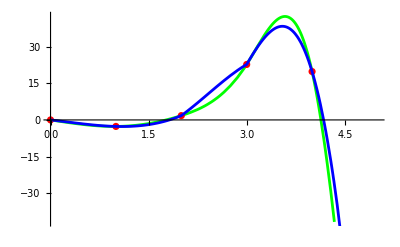

Set::wrsym: Symbol Factor is Protected.

Part::partw: Part 2 of SplineFunction[[0.000102143 factor] does not exist.

Part::partw: Part 2 of SplineFunction[[0.102143 factor] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

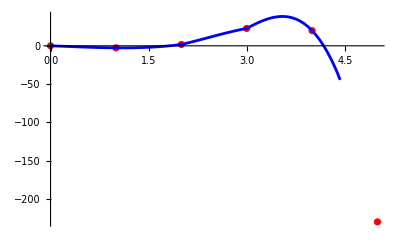

```mathematica
Needs["Splines`"]
(*zad3*)
data6 = {{0,0},{1,-2.66},{2,1.76},{3,22.68},{4,19.78},{5,-229.61}};
t = Interpolation[data6,InterpolationOrder->3]
plot3 = Plot[t[x],{x,0,5},PlotStyle->Blue];
sf = SplineFit[data6,Cubic]
factor = 5/(5.0-0.0);
s[x_] := sf[factor x][ [2]];
plot1 = Plot[s[x],{x,0,5},PlotStyle->Green];
plot2 = ListPlot[data6,PlotStyle -> Red];
Show[plot1,plot2,plot3]
```

```mathematica
(*zad3*)
SeedRandom[1];
g[x_] := 25.25 - 40(x^2) + 200e^(-0.5*x);
datagen := Table[x,g[x]+RandomReal[NormalDistribution[0,1.0]],{x,-10,10,1}]
Print("No. of data points: ",ngen=Length[datagen])
dataplot = ListPlot[datagen,PlotStyle->Red,PlotRange->All];
```

Table::nliter: Non-list iterator g[x]+RandomReal[NormalDistribution[0,1.]] at position 2 does not evaluate to a real numeric value.

Table[x,g[x]+RandomReal[NormalDistribution[0,1.]],{x,-10,10,1}]

```mathematica
Table[x,g[x]+RandomReal[NormalDistribution[0,1.0]],{x,-10,10,1}]
```

```mathematica
Table[{x,g[x]+RandomReal[NormalDistribution[0,1.0]]},{x,-10,10,1}]

(*zad4*)
ClearAll
SeedRandom[1]
g[x_] = 25.25 - 40*(x^2) + 200 ⅇ^(-0.5x)
datagen = Table[x,g[x]+RandomReal[NormalDistribution[0,1.0]],{x,-10,10,1}]
linearfun[x_] = Fit[datagen,{1,x^2,ⅇ^-x},x]
linearplot = Plot[linearfun[x],{x,-10,10},PlotStyle -> Green, PlotRange -> All]
```

{{-10,25707.3},{-9,14786.7},{-8,8385.78},{-7,4686.61},{-6,2602.17},{-5,1461.82},{-4,863.196},{-3,561.683},{-2,407.657},{-1,315.126},{0,225.135},{1,105.927},{2,-61.202},{3,-290.914},{4,-588.294},{5,-960.94},{6,-1403.32},{7,-1929.28},{8,-2529.64},{9,-3213.2},{10,-3973.25}}

ClearAll

RandomGeneratorState[…]

```mathematica
g[x_]=25.25+200 ⅇ^(-0.5 x)-40 x^2
```

Table::nliter: Non-list iterator g[x]+RandomReal[NormalDistribution[0,1.]] at position 2 does not evaluate to a real numeric value.

```mathematica
datagen = Table[x,g[x]+RandomReal[NormalDistribution[0,1.0]],{x,-10,10,1}]
form = a+ bx^2+ cⅇ^-dx
```

Table::nliter: Non-list iterator g[x]+RandomReal[NormalDistribution[0,1.]] at position 2 does not evaluate to a real numeric value.

```mathematica
nonlinparams = FindFit[datagen,form,{a,b,c,d},x]
```

```mathematica
nonlinearfun[x_] = form /. nonlinparams
nonlinearplot = Plot[nonlinearfun[x],{x,-10,10},PlotStyle -> Brown]
(*Exercise 4*)

ClearAll[]
```

ReplaceAll::reps: {nonlinparams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

form/.nonlinparams

-Graphics-

-Graphics-